{{51.39,13.28},{53.36,11.96},{55.5,10.64},{57.64,9.98},{59.61,9.65},{60.6,9.32},{61.92,9.32},{62.9,9.32},{63.23,9.32},{63.89,9.31},{64.22,8.98},{64.54,8.97},{64.54,8.97},{64.87,8.96},{64.87,8.95},{64.87,8.95},{65.19,8.62},{65.19,8.94},{65.19,9.27},{65.51,9.26},{65.5,9.26},{65.51,9.58},{65.83,9.91},{66.16,9.9},{66.49,10.23},{67.14,10.56},{67.46,11.53},{68.12,11.86},{69.1,12.84},{70.09,13.83},{72.06,14.48},{76.17,17.11},{80.29,18.43},{86.05,21.06},{91.81,24.19},{98.56,25.34},{105.96,26.99},{114.68,27.65},{119.62,27.98},{129.16,25.67},{137.05,22.38},{146.92,19.43},{156.8,16.79},{166.34,13.5},{175.55,12.19},{184.77,10.54},{191.35,9.88},{196.94,10.21},{202.21,9.22},{204.51,8.89},{207.15,8.23},{206.49,7.25},{207.47,6.92},{208.79,5.6}}

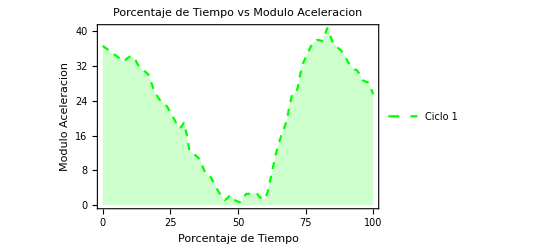

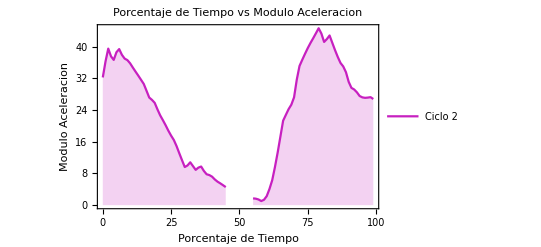

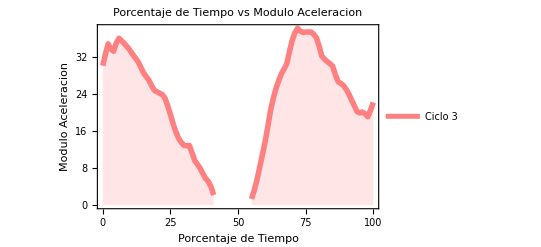

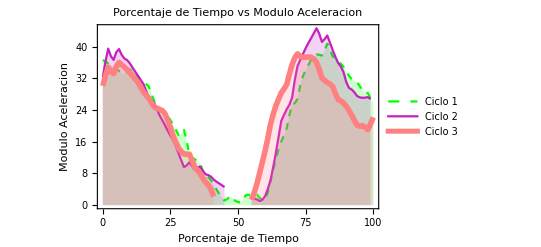

```mathematica
(*Importamos el archivo excel*)
e = Import["E:\\Users\\Almanzor\\Documents\\Escuela\\Biomecanica\\Examen 2\\Valores juntos1.xlsx"][[1]];
(*Medimos la longitud del arreglo para saber la duracion de los ciclos*)
LongitudDeArreglo = Length[e];
(*Separamos cada componente de tobillo, rodilla y cadera en vectores, X, Y*)
(*Ciclo 1*)
PosicionTobilloEnX1=Table[{e[[i,2]]},{i,2,LongitudDeArreglo}];
PosicionTobilloEnY1=Table[{e[[i,3]]},{i,2,LongitudDeArreglo}];
PosicionRodillaEnX1=Table[{e[[i,4]]},{i,2,LongitudDeArreglo}];
PosicionRodillaEnY1=Table[{e[[i,5]]},{i,2,LongitudDeArreglo}];
PosicionCaderaEnX1=Table[{e[[i,6]]},{i,2,LongitudDeArreglo}];
PosicionCaderaEnY1=Table[{e[[i,7]]},{i,2,LongitudDeArreglo}];
(*Ciclo 2*)
PosicionTobilloEnX2=Table[{e[[i,9]]},{i,2,LongitudDeArreglo}];
PosicionTobilloEnY2=Table[{e[[i,10]]},{i,2,LongitudDeArreglo}];
PosicionRodillaEnX2=Table[{e[[i,11]]},{i,2,LongitudDeArreglo}];
PosicionRodillaEnY2=Table[{e[[i,12]]},{i,2,LongitudDeArreglo}];
PosicionCaderaEnX2=Table[{e[[i,13]]},{i,2,LongitudDeArreglo}];
PosicionCaderaEnY2=Table[{e[[i,14]]},{i,2,LongitudDeArreglo}];
(*Ciclo 3*)
PosicionTobilloEnX3=Table[{e[[i,16]]},{i,2,LongitudDeArreglo}];
PosicionTobilloEnY3=Table[{e[[i,17]]},{i,2,LongitudDeArreglo}];
PosicionRodillaEnX3=Table[{e[[i,18]]},{i,2,LongitudDeArreglo}];
PosicionRodillaEnY3=Table[{e[[i,19]]},{i,2,LongitudDeArreglo}];
PosicionCaderaEnX3=Table[{e[[i,20]]},{i,2,LongitudDeArreglo}];
PosicionCaderaEnY3=Table[{e[[i,21]]},{i,2,LongitudDeArreglo}];
(*Tambien extraigo el vector tiempo*)
Tiempo1 =Table[{e[[i,1]]},{i,2,LongitudDeArreglo}];
Tiempo2 =Table[{e[[i,8]]},{i,2,LongitudDeArreglo}];
Tiempo3 =Table[{e[[i,15]]},{i,2,LongitudDeArreglo}];
(*Junto cada componente de la posicion en un vector para cada ciclo*)
VectorPosicionTobillo1 = Table[{PosicionTobilloEnX1[[i,1]],PosicionTobilloEnY1[[i,1]]},{i,1,LongitudDeArreglo-1}]
VectorPosicionRodilla1 = Table[{PosicionRodillaEnX1[[i,1]],PosicionRodillaEnY1[[i,1]]},{i,1,LongitudDeArreglo-1}];
VectorPosicionCadera1 = Table[{PosicionCaderaEnX1[[i,1]],PosicionCaderaEnY1[[i,1]]},{i,1,LongitudDeArreglo-1}];
VectorPosicionTobillo2 = Table[{PosicionTobilloEnX2[[i,1]],PosicionTobilloEnY2[[i,1]]},{i,1,LongitudDeArreglo-1}];
VectorPosicionRodilla2 = Table[{PosicionRodillaEnX2[[i,1]],PosicionRodillaEnY2[[i,1]]},{i,1,LongitudDeArreglo-1}];
VectorPosicionCadera2 = Table[{PosicionCaderaEnX2[[i,1]],PosicionCaderaEnY2[[i,1]]},{i,1,LongitudDeArreglo-1}];
VectorPosicionTobillo3 = Table[{PosicionTobilloEnX3[[i,1]],PosicionTobilloEnY3[[i,1]]},{i,1,LongitudDeArreglo-1}];
VectorPosicionRodilla3 = Table[{PosicionRodillaEnX3[[i,1]],PosicionRodillaEnY3[[i,1]]},{i,1,LongitudDeArreglo-1}];
VectorPosicionCadera3 = Table[{PosicionCaderaEnX3[[i,1]],PosicionCaderaEnY3[[i,1]]},{i,1,LongitudDeArreglo-1}];
(*Calculamos el vector Cadera menos rodilla*)
VectorCaderaRodilla1 = Table[{VectorPosicionCadera1 [[i,1]]-VectorPosicionRodilla1[[i,1]],VectorPosicionCadera1 [[i,2]]-VectorPosicionRodilla1[[i,2]]},{i,1,LongitudDeArreglo-1}];
VectorCaderaRodilla2 = Table[{VectorPosicionCadera2[[i,1]]-VectorPosicionRodilla2[[i,1]],VectorPosicionCadera2[[i,2]]-VectorPosicionRodilla2[[i,2]]},{i,1,LongitudDeArreglo-1}];
VectorCaderaRodilla3 = Table[{VectorPosicionCadera3[[i,1]]-VectorPosicionRodilla3[[i,1]],VectorPosicionCadera3 [[i,2]]-VectorPosicionRodilla3[[i,2]]},{i,1,LongitudDeArreglo-1}];
(*Calculo los modulos de l vector rodilla cadera*)
ModuloVectorCaderaRodilla1=Table[{Norm[VectorCaderaRodilla1[[i]]]},{i,1,LongitudDeArreglo-1}];
ModuloVectorCaderaRodilla2=Table[{Norm[VectorCaderaRodilla1[[i]]]},{i,1,LongitudDeArreglo-1}];
ModuloVectorCaderaRodilla3=Table[{Norm[VectorCaderaRodilla1[[i]]]},{i,1,LongitudDeArreglo-1}];
(*Calculo el angulo siguiendo la ley de pitagoraspara suponer un triangulo entre la horizontal y mi vector de posicion, despues uso ley de cosenos para calcular el angulo con los valores de los secmentos del triangulo*)
VectorAngulo1 = Table[{ArcCos[(VectorCaderaRodilla1[[i,1]]^2-(VectorCaderaRodilla1[[i,2]]^2+ModuloVectorCaderaRodilla1[[i,1]]^2))/(-2*VectorCaderaRodilla1[[i,2]]*ModuloVectorCaderaRodilla1[[i,1]])]/Degree},{i,1,LongitudDeArreglo-1}];
VectorAngulo2 = Table[{ArcCos[(VectorCaderaRodilla2[[i,1]]^2-(VectorCaderaRodilla2[[i,2]]^2+ModuloVectorCaderaRodilla2[[i,1]]^2))/(-2*VectorCaderaRodilla2[[i,2]]*ModuloVectorCaderaRodilla2[[i,1]])]/Degree},{i,1,LongitudDeArreglo-1}];
VectorAngulo3 = Table[{ArcCos[(VectorCaderaRodilla3[[i,1]]^2-(VectorCaderaRodilla3[[i,2]]^2+ModuloVectorCaderaRodilla3[[i,1]]^2))/(-2*VectorCaderaRodilla3[[i,2]]*ModuloVectorCaderaRodilla3[[i,1]])]/Degree},{i,1,LongitudDeArreglo-1}];

TiempoVsVectorAngulo1= Table[{Tiempo1[[i,1]],VectorAngulo1[[i,1]]},{i,1,LongitudDeArreglo-1}];
TiempoVsVectorAngulo2= Table[{Tiempo2[[i,1]],VectorAngulo2[[i,1]]},{i,1,LongitudDeArreglo-1}];
TiempoVsVectorAngulo3= Table[{Tiempo3[[i,1]],VectorAngulo3[[i,1]]},{i,1,LongitudDeArreglo-1}];
(*Vamos a graficar como si el movimiento fuera de 0 a 100 para eso calculamos el incremento
con la cantidad final del tiempo menos la inicial entre 100*)
Incremento=(e[[LongitudDeArreglo,1]]-e[[2,1]])/100;
(*La interpolacion crea una funcion de la variable TiempoVsModuloAceleracion en la que podemos evaluar la variable*)
PorcentajeDeTiempoVsVectorAngulo1 = Interpolation[TiempoVsVectorAngulo1,InterpolationOrder->1];
PorcentajeDeTiempoVsVectorAngulo2 = Interpolation[TiempoVsVectorAngulo2,InterpolationOrder->1];
PorcentajeDeTiempoVsVectorAngulo3 = Interpolation[TiempoVsVectorAngulo3,InterpolationOrder->1];

(*Armamos una tabla nueva con el eje x en porcentaje y el eje Y con la funcion de interpolacion*)
TablaPorcentajeDeTiempoVsVectorAngulo1 =Table[{(i/Incremento),PorcentajeDeTiempoVsVectorAngulo1[i]},{i,TiempoVsVectorAngulo1[[1,1]],TiempoVsVectorAngulo1[[LongitudDeArreglo-1,1]],Incremento}];
TablaPorcentajeDeTiempoVsVectorAngulo2=Table[{(i/Incremento),PorcentajeDeTiempoVsVectorAngulo2[i]},{i,TiempoVsVectorAngulo2[[1,1]],TiempoVsVectorAngulo2[[LongitudDeArreglo-1,1]],Incremento}];
TablaPorcentajeDeTiempoVsVectorAngulo3=Table[{(i/Incremento),PorcentajeDeTiempoVsVectorAngulo3[i]},{i,TiempoVsVectorAngulo3[[1,1]],TiempoVsVectorAngulo3[[LongitudDeArreglo-1,1]],Incremento}];

(*Graficamos el Ciclo 1*)
GraficaCiclo1Completo=ListPlot[{TablaPorcentajeDeTiempoVsVectorAngulo1},Joined->True,Filling->Axis,PlotStyle->{{Green,Glow,Dashed}},Frame->True,FrameLabel->{"Porcentaje de Tiempo","Modulo Aceleracion"},PlotLegends->{"Ciclo 1"},PlotLabel->"Porcentaje de Tiempo vs Modulo Aceleracion"]
(*Graficamos el Ciclo 2*)
GraficaCiclo2Completo=ListPlot[{TablaPorcentajeDeTiempoVsVectorAngulo2},Joined->True,Filling->Axis,PlotStyle->{{Purple,Glow,Hue[0.84,0.84,0.78]}},Frame->True,FrameLabel->{"Porcentaje de Tiempo","Modulo Aceleracion"},PlotLegends->{"Ciclo 2"},PlotLabel->"Porcentaje de Tiempo vs Modulo Aceleracion"]
(*Graficamos el Ciclo 3*)
GraficaCiclo3Completo=ListPlot[{TablaPorcentajeDeTiempoVsVectorAngulo3},Joined->True,Filling->Axis,PlotStyle->{{Pink,Glow,Thickness[0.01]}},Frame->True,FrameLabel->{"Porcentaje de Tiempo","Modulo Aceleracion"},PlotLegends->{"Ciclo 3"},PlotLabel->"Porcentaje de Tiempo vs Modulo Aceleracion"]
(*Graficamos los tres Ciclos en una sola grafica*)

Show[{GraficaCiclo1Completo,GraficaCiclo2Completo,GraficaCiclo3Completo},PlotRange->All]
Export["E:\\Users\\Almanzor\\Documents\\Escuela\\Biomecanica\\Practicas\\TablaPorcentajeDeTiempoVsVectorAngulo1.xls",TablaPorcentajeDeTiempoVsVectorAngulo1];
```